# MutualInformation

This function computes the Mutual Information of a multivariate distribution or samples of data using the Kraskov estimator

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

Computes the mutual information for a bivariate distribution. First I set some options.

```mathematica
Options[MutualInformation]={"CopulaKernel"-> "Product","Marginals"->Automatic,DistanceFunction->ChessboardDistance, "Errors"->False, "KNeighbour"->4, "Parallelize"->False};;
Options[KraskovI1]=Options[KraskovI1DM]=Options[MutualInformationError]={DistanceFunction->ChessboardDistance, "KNeighbour"->4, "Parallelize"->False};
```

Computes Mutual Information for a joint probability distribution distz

Update: now it works on multivariate distributions.

```mathematica
MutualInformation::jointdist="Distribution domain `1` is invalid. Please provide a multivariate distribution.";
MutualInformation::marginals="Value `1` for option `2` is invalid. Please provide a valid integer, a list of integer or Automatic.";
MutualInformation::splitlist="List `1` is must be a subset of `2`. Please provide a valid list.";
MutualInformation::copuladist="Distribution `1` must satisfy DistributionParameterQ test.";
MutualInformation::kneigh="The option KNeighbour expects an integer.";
MutualInformation::len="The lenght of the two lists provided doesn't match.";
MutualInformation::lstlen="The length of the list should be greater than `1`";
MutualInformation::distances="The option DistanceFunction accepts only one or two distances in a list.";
```

```mathematica
MutualInformation[distz_?DistributionParameterQ, opts:OptionsPattern[{Options[ResourceFunction["KullbackLeiblerDivergence"]],MutualInformation}]]:=
With[{domainz=DistributionDomain[distz], dim=Length[DistributionDomain[distz]]},
Module[{productDist,distx,disty, splt=ReplaceAll[OptionValue[MutualInformation,"Marginals"],{l:{___}:>l,i_Integer:>{i}}]},

If[dim≤1,Message[MutualInformation::jointdist,domainz];Return[$Failed]];
Switch[splt,Automatic,{distx,disty}=With[{splitHalf=Round[dim/2]},Map[MarginalDistribution[distz,#]&,{Range[splitHalf],Range[splitHalf+1,dim]}]],{__Integer}/;(SubsetQ[Range[dim],splt]),{distx,disty}=Map[MarginalDistribution[distz,#]&,{splt,Complement[Range[dim],splt]}],
{__Integer},Message[MutualInformation::splitlist,splt,Range[dim]];Return[$Failed],
_,Message[MutualInformation::marginals,splt,"Marginals"];Return[$Failed]];

(* this bit of code is needed to fix the behaviour of LogLikelihood for the ProductDistribution of multivariate distributions *)
productDist/:LogLikelihood[productDist[p_,q_],{vars_List}]/;(AllTrue[{DistributionDomain[p],DistributionDomain[q]},ArrayQ]):=Simplify[LogLikelihood[p,{Take[vars,Length[DistributionDomain[p]]]}]+LogLikelihood[q,{Drop[vars,Length[DistributionDomain[p]]]}]];
productDist/:LogLikelihood[productDist[p_,q_],{vars_}]:=Simplify[LogLikelihood[ProductDistribution[p,q],{vars}]];
productDist/:f_[productDist[p_,q_]]:=f[ProductDistribution[p,q]];

ResourceFunction["KullbackLeiblerDivergence"][distz,productDist[distx,disty], FilterRules[{opts},Options[ResourceFunction["KullbackLeiblerDivergence"]]]]
]];
```

Computes the mutual information from two marginal distributions, considering their copula distribution for the joint space.

```mathematica
MutualInformation[distx_?DistributionParameterQ, disty_?DistributionParameterQ, opts:OptionsPattern[{Options[ResourceFunction["KullbackLeiblerDivergence"]],MutualInformation}]]:=
With[{distz=CopulaDistribution[OptionValue[MutualInformation,"CopulaKernel"],{distx,disty}]},
Module[{productDist},

If[!DistributionParameterQ[distz],Message[MutualInformation::copuladist,distz];Return[$Failed]];

productDist/:LogLikelihood[productDist[p_,q_],{vars_List}]/;(AllTrue[{DistributionDomain[p],DistributionDomain[q]},ArrayQ]):=Simplify[LogLikelihood[p,{Take[vars,Length[DistributionDomain[p]]]}]+LogLikelihood[q,{Drop[vars,Length[DistributionDomain[p]]]}]];
productDist/:LogLikelihood[productDist[p_,q_],{vars_}]:=Simplify[LogLikelihood[ProductDistribution[p,q],{vars}]];
productDist/:f_[productDist[p_,q_]]:=f[ProductDistribution[p,q]];

ResourceFunction["KullbackLeiblerDivergence"][distz,productDist[distx,disty], FilterRules[{opts},Options[ResourceFunction["KullbackLeiblerDivergence"]]]]
]];
```

The following computes the mutual information using the Kraskov first estimator. I use two implementations of the estimator, one is naive the other is faster but runs out of memory for 100,000 data points, so I switch between them at the empirical value of 10,000.

The parameter k is the order of the neighbour, the best value overall is given by k=4.

```mathematica
distancePattern=Alternatives[_Symbol,_Function,Sequence@@Tuples[{_Symbol,_Function},2]];
```

```mathematica
Condition[MutualInformation[x_List,y_List,opts:OptionsPattern[MutualInformation]],Length[x]==Length[y]]:=(
If[!IntegerQ[OptionValue[MutualInformation,"KNeighbour"]],Message[MutualInformation::kneigh];Return[$Failed]];Switch[OptionValue[MutualInformation,DistanceFunction],distancePattern,Null, _,Message[MutualInformation::distances];Return[$Failed]];

Switch[Length[x]<10000,
True,Around[KraskovI1DM[x,y,FilterRules[{opts},Options[KraskovI1DM]]],
If[OptionValue[MutualInformation,"Errors"],
MutualInformationError[KraskovI1DM,x,y,FilterRules[{opts},Options[MutualInformationError]]],0.]],
False,Around[KraskovI1[x,y,FilterRules[{opts},Options[KraskovI1]]],
If[OptionValue[MutualInformation,"Errors"],
MutualInformationError[KraskovI1,x,y,FilterRules[{opts},Options[MutualInformationError]]],0.]]]
);
```

```mathematica
MutualInformation[x_List,y_List,___]:=Catch[Message[MutualInformation::len];Throw[$Failed]];
```

Computes the auto mutual information for a list at shifts up to t or at {t_1,t_2,…}.

```mathematica
(* computes the mutual information between batches of data at shifts Range[0,T] *)
```

```mathematica
Condition[MutualInformation[x_List,T_Integer,opts:OptionsPattern[MutualInformation]],Length[x]>T]:=
With[{n=Length[x],optf=FilterRules[{opts},Options[MutualInformation]]},
If[!IntegerQ[OptionValue[MutualInformation,"KNeighbour"]],Message[MutualInformation::kneigh];Return[$Failed]];
Switch[OptionValue[MutualInformation,DistanceFunction],distancePattern,Null, _,Message[MutualInformation::distances];Return[$Failed]];
Map[MutualInformation[x⟦;;(n-T)⟧,x⟦(#+1);;(#+n-T)⟧,optf]&,Range[0,T]]
];
```

```mathematica
MutualInformation[x_List,T_Integer,___]:=Catch[Message[MutualInformation::lstlen,T];Throw[$Failed]];
```

```mathematica
(* computes the mutual information between batches of data at shifts {T1,T2, etc.} *)
```

```mathematica
Condition[MutualInformation[x_List,T:{__Integer},opts:OptionsPattern[MutualInformation]],Length[x]>Max[T]]:=With[{n=Length[x],TMax=Max[T],optf=FilterRules[{opts},Options[MutualInformation]]},
If[!IntegerQ[OptionValue[MutualInformation,"KNeighbour"]],Message[MutualInformation::kneigh];Return[$Failed]];
Switch[OptionValue[MutualInformation,DistanceFunction],distancePattern,Null, _,Message[MutualInformation::distances];Return[$Failed]];
Map[MutualInformation[x⟦;;(n-TMax)⟧,x⟦(#+1);;(#+n-TMax)⟧,optf]&,T]
];
```

```mathematica
MutualInformation[x_List,T:{__Integer},___]:=Catch[Message[MutualInformation::lstlen,Max[T]];Throw[$Failed]];
```

```mathematica
(* computes the mutual information between batches of length T at fixed shift S *)
```

```mathematica
Condition[MutualInformation[x_List,T_Integer,S_Integer,opts:OptionsPattern[MutualInformation]],Length[x]>(T+S)]:=
With[{n=Length[x],optf=FilterRules[{opts},Options[MutualInformation]]},If[!IntegerQ[OptionValue[MutualInformation,"KNeighbour"]],Message[MutualInformation::kneigh];Return[$Failed]];Switch[OptionValue[MutualInformation,DistanceFunction],distancePattern,Null, _,Message[MutualInformation::distances];Return[$Failed]];Map[MutualInformation[x⟦#;;(#+T)⟧,x⟦(#+S);;(#+T+S)⟧,optf]&,Range[0,n-T-S]]
];
```

```mathematica
MutualInformation[x_List,T_Integer,S_Integer,___]:=Catch[Message[MutualInformation::listlen,T+S];Throw[$Failed]];
```

Error estimator. Uses an extrapolation to estimate the statistical error for the sample size.

```mathematica
Condition[MutualInformationError[miEstimator_,x_List,y_List,opts:OptionsPattern[MutualInformationError]],Length[x]==Length[y]]:=With[{NT=Length[x],n=Range[2,10],optf=FilterRules[{opts},Options[miEstimator]]},Module[{xyn=Transpose[{x,y}],minfo,varni},minfo=Map[miEstimator[#[[All,1]],#[[All,2]],optf]&,Take[Partition[xyn,UpTo[Round[NT/#]]],#]&/@n,{2}];varni=Variance/@minfo;Sqrt[Total[((n-1)/n)*varni]/Total[(n-1)]]
]];
```

Compiling this function saves a few tenths of a second on large lists. Used in both implementations below.

```mathematica
Quiet@LaunchKernels[];

Quiet[polyCompiled=Compile[{k,n,nx,ny},
PolyGamma[k]+PolyGamma[n]-PolyGamma[nx]-PolyGamma[ny],
CompilationTarget->"C",
RuntimeAttributes->{Listable},
CompilationOptions->{"InlineExternalDefinitions" -> True}
]];
```

Kraskov estimator, naive implementation. The main function uses this for data larger than 10,000 data points.

```mathematica
KraskovI1[x_List,y_List,OptionsPattern[KraskovI1]]:=
With[{xyn=Transpose[{x,y}],n=Length[x],k=OptionValue[KraskovI1,"KNeighbour"],distX=Part[OptionValue[KraskovI1,DistanceFunction],1],distY=Part[OptionValue[KraskovI1,DistanceFunction],-1]},
Module[{distZ,distances,nx,ny},
(* efficiency: if the distance in X and Y is the Chessboard distance, just use the same built in distance in Z=(X,Y) *)
If[SameQ[distX,distY,ChessboardDistance],distZ=ChessboardDistance,distZ=(Max[distX[#1⟦1⟧,#2⟦1⟧],distY[#1⟦2⟧,#2⟦2⟧]]&)];

(* calculate the distance of each z[i] from it's k-th neighbour in Z, picks only the k-th result *)
distances=Nearest[xyn->"Distance",xyn,k+1,DistanceFunction->distZ]⟦All,-1⟧;

(* counts how many points are inside balls of certain distances, for each point in X and Y *)
{nx,ny}=Transpose[
If[OptionValue[KraskovI1,"Parallelize"],
Parallelize,Sequence][
MapThread[{Length[Nearest[x,#1,{All,#3},DistanceFunction->distX]],Length[Nearest[y,#2,{All,#3},DistanceFunction->distY]]}&,{x,y,distances}]
]];

(* estimation of mutual information *)
Mean@polyCompiled[k,n,nx,ny]
]];
```

Kraskov estimator, faster implementation. It runs out of memory for data with more than 100,000 data points and significantly slows down for more than 10,000 data points, so the above implementation is used in such cases. It is much faster on high dimensional data, like lists of images and such.

```mathematica
KraskovI1DM[x_List,y_List,opts:OptionsPattern[KraskovI1DM]]:=With[{xyn=Transpose[{x,y}],n=Length[x],k=OptionValue[KraskovI1DM,"KNeighbour"],distX=Part[OptionValue[KraskovI1DM,DistanceFunction],1],distY=Part[OptionValue[KraskovI1DM,DistanceFunction],-1]},
Module[{distancesX,distancesY,distances,nx,ny},

(* calculates the distance of each x[i] from it's k-th neighbour, picks only the k-th result *)
distancesX=DistanceMatrix[x,DistanceFunction->distX];
distancesY=DistanceMatrix[y,DistanceFunction->distY];
distances=Check[Ramp[Subtract[distancesX,distancesY]]+distancesY,$Failed];distances=(Nearest[#,0.,k+1]&/@distances)⟦All,-1⟧;

(* counts how many points are inside balls of certain distances, for each value in X and Y *)
{nx,ny}=Transpose[
If[OptionValue[KraskovI1DM,"Parallelize"],
Parallelize,Sequence][
MapThread[{Length[Nearest[#1,0.,{All,#3}]],Length[Nearest[#2,0.,{All,#3}]]}&,{distancesX,distancesY,distances}]
]];

(* estimation of mutual information *)
Mean@polyCompiled[k,n,nx,ny]
]];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

Nice Function! Thank you for submitting it. We added a few questions and comments below. Please address them and submit and update.

MutualInformation[list, list]

estimates the mutual information from two lists of elements.

MutualInformation[list,t]

estimates the auto-mutual on a list of elements, comparing batches of elements at shifts given by Range[0, t].

MutualInformation[list, t, s]

estimates the auto-mutual on a list of elements, comparing running batches of length t at a fixed shift s.

MutualInformation[dist]

computes the mutual information of a bivariate distribution dist.

MutualInformation[distx, disty]

computes the mutual information of the bivariate distribution given by CopulaDistribution[ker, {distx, disty}].

Could you easily support MutualInformation[list] by having a default t?

I could, but I don't think that would be useful. Take as an example CorrelationFunction[data,hspec], which does the same thing but for the correlation, it wouldn't make much sense to give hspec a default value.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

Please explain that this uses parallel kernels by default. It would be nice to make the parallelization optional.

I added an option "Parallelize" to the estimators (the ones working with lists) and specified it below.

The estimator MutualInformation[list, t] computes the mutual information between list[i] and list[i+s], with s∈Range[0,t].

The function uses parallel kernels by default. To force sequential execution, just use the option value "Parallelize"→False.

In MutualInformation[list,t] the parameter t can be either an integer or a list of integers.

Default options for MutualInformation[list, ___] are:

DistanceFunction | ChessboardDistance | distance used to compute the estimator
"Errors" | False | whether to compute or not the error on the estimator
“KNeighbour” | 4 | kth-nearest neighbour parameter to be used for the estimator
"Parallelize" | True | whether to use parallel computation or not

MutualInformation[list, list] and MutualInformation[list, t] both use an estimator which relies on a kth-nearest neighbours algorithm. The default value of k is 4, to set a different use the option “KNeighbour” with an integer value. See the source material for more information.

The function MutualInformation[dist] expects a multivariate distribution.

The functions MutualInformation[dist] and MutualInformation[distx, disty] both rely on ResourceFunction[“KullbackLeiblerDivergence”] to work, hence both accept the same options as ResourceFunction[“KullbackLeiblerDivergence”].

Default options for MutualInformation[dist] (options belonging to ResourceFunction[“KullbackLeiblerDivergence”] are not shown):

"Marginals" | Automatic | how to extract marginals from the joint distribution

The option "Marginals"->Automatic splits the joint space in half.

Default options for MutualInformation[dist,dist] (options belonging to ResourceFunction[“KullbackLeiblerDivergence”] are not shown):

“CopulaKernel” | “Product” | uses the specified copula kernel to compute the bivariate distribution

Any kernel supported by CopulaDistribution, though some copulas will be hard to compute exactly. Use the option Method->NExpectation (provided by ResourceFunction[“KullbackLeiblerDivergence”]) to compute a numerical approximation.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

Please add error handling for this case, so that it does not return such a big mess.


"[◼]" | "MutualInformation" [GammaDistribution[2,1],NormalDistribution[5,2]]
NIntegrate::inumri: "The integrand Log[Piecewise[{{1, FunctionRepository`$244c192287144160a5ddba4b25d05347`x>0}, {Indeterminate, True}}]] (Piecewise[{{(ⅇ^(Times[«2»]+Times[«2»]) FunctionRepository`$244c192287144160a5ddba4b25d05347`x)/(2 √(2 π)), FunctionRepository`$244c192287144160a5ddba4b25d05347`x>0}, {0, True}}]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-∞,0.},{∞,0.}}."
NIntegrate[PDF[CopulaDistribution["Product",{GammaDistribution[2,1],NormalDistribution[5,2]}],{FunctionRepository`$244c192287144160a5ddba4b25d05347`x,FunctionRepository`$244c192287144160a5ddba4b25d05347`y}] Log[Simplify[PDF[CopulaDistribution["Product",{GammaDistribution[2,1],NormalDistribution[5,2]}],{FunctionRepository`$244c192287144160a5ddba4b25d05347`x,FunctionRepository`$244c192287144160a5ddba4b25d05347`y}]/(PDF[GammaDistribution[2,1],FunctionRepository`$244c192287144160a5ddba4b25d05347`x] PDF[NormalDistribution[5,2],FunctionRepository`$244c192287144160a5ddba4b25d05347`y])]],{FunctionRepository`$244c192287144160a5ddba4b25d05347`x,-∞,∞},{FunctionRepository`$244c192287144160a5ddba4b25d05347`y,-∞,∞},AccuracyGoal→OptionValue["[◼]" | "MutualInformation" ,{},AccuracyGoal]]

I would like to update my function for the case of probability distributions, by using the repository function ResourceFunction[“KullbackLeiblerDivergence”], which has already a lot of error checking. Mine would just call this function with the correct arguments. However, while testing this route I run into an issue: consider the code

```mathematica
ResourceFunction["KullbackLeiblerDivergence"][BinormalDistribution[0.8],ProductDistribution[NormalDistribution[0.,1.],NormalDistribution[0.,1.]],Method->NExpectation]
```

NIntegrate::write: Tag x in x[1] is Protected.

NExpectation[0.510826-0.888889 x[1]^2+2.22222 x[1] x[2]-0.888889 x[2]^2,{x[1],x[2]}\[Distributed]BinormalDistribution[0.8]]

and compare it to

```mathematica
ResourceFunction["KullbackLeiblerDivergence"][BinormalDistribution[0.8],ProductDistribution[NormalDistribution[0.,1.],NormalDistribution[0.,1.]]]
```

0.510826

I need the option Method→NExpectation to make it work, since the exact computation uses Expectation and can be cumbersome on some distributions (this example is taken from the function's documentation):

```mathematica
TimeConstrained[ResourceFunction["KullbackLeiblerDivergence"][NormalDistribution[0.,1.],StableDistribution[1,1.3,0.5,0.,2.]],10]
```

$Aborted

The issue you noted is now reported as a bug. Meanwhile, it would be best for you to make the changes that use ResourceFunction[“KullbackLeiblerDivergence”] (with the  Method→NExpectation setting as needed), and we will live with the problems this might give until they are fixed.

I updated the functions MutualInformation[dist] and MutualInformation[dist,dist], now they both use ResourceFunction[“KullbackLeiblerDivergence”]. Note: I had to add a bit of extra code to fix the behaviour of LogLikelihood when it is supplied a ProductDistribution of two multivariate distribution, see below for a brief explanation.

```mathematica
(* Code *)
Module[{productDist},
productDist/:LogLikelihood[productDist[p_,q_],{vars_List}]/;(AllTrue[{DistributionDomain[p],DistributionDomain[q]},ArrayQ]):=Simplify[LogLikelihood[p,{Take[vars,Length[DistributionDomain[p]]]}]+LogLikelihood[q,{Drop[vars,Length[DistributionDomain[p]]]}]];
productDist/:LogLikelihood[productDist[p_,q_],{vars_}]:=Simplify[LogLikelihood[ProductDistribution[p,q],{vars}]];
productDist/:f_[productDist[p_,q_]]:=f[ProductDistribution[p,q]];
];
```

I need to use MarginalDistribution[dist,{1,2,...}] with a list of integers (even if dist is bivariate), in order to work with general multivariate distributions. 
If I use this on a simple bivariate distribution:

```mathematica
MarginalDistribution[BinormalDistribution[0.1],{1}]
```

MultinormalDistribution[{0},{{1}}]

This is a univariate distribution, but is considered multivariate by Mathematica. This causes an issue:

```mathematica
LogLikelihood[ProductDistribution[MultinormalDistribution[{0},{{1}}],MultinormalDistribution[{0},{{1}}]],{{x,y}}]
```

LogLikelihood[MultinormalDistribution[{0},{{1}}],{x}]+LogLikelihood[MultinormalDistribution[{0},{{1}}],{y}]

```mathematica
(* Notice that MultinormalDistribution[{0},{{1}}] is just NormalDistribution[] *)
```

```mathematica
LogLikelihood[ProductDistribution[NormalDistribution[],NormalDistribution[]],{{x,y}}]
```

-x^2/2-y^2/2-Log[2]-Log[π]

This computation is at the core of ResourceFunction[“KullbackLeiblerDivergence”]. Instead of pasting the whole code of ResourceFunction[“KullbackLeiblerDivergence”] in my function to fix this specific thing, I opted for the code above which defines an upvalue for "productDist", a symbol scoped in my function, and forces the right behaviour on LogLikelihood. Please, notify me whether this is acceptable or not.

Note: I also fixed some minor things and added a few functionalities. Remains to fix the Method→NExpectation bug.

### Basic Examples

Compute the mutual information of a binormal distribution:

```mathematica
MutualInformation[BinormalDistribution[0.8]]
```

0.510826

Compare it to its real value:

```mathematica
-1/2 Log[1-0.8^2]
```

0.510826

It can be computed using a symbolic distribution, too:

```mathematica
MutualInformation[BinormalDistribution[ρ]]
```

-1/2 Log[1-ρ^2]

Compute the mutual information of a more complex multivariate distribution:

```mathematica
MutualInformation[MultinormalDistribution[{1,2,3},{{2,1/2,-1/3},{1/2,1,0},{-1/3,0,2/3}}],"Marginals"->{1,2}]
```

1/2 Log[21/19]

Compute the mutual information of a bivariate distribution, starting from the two marginal distribution:

```mathematica
MutualInformation[NormalDistribution[2,1],NormalDistribution[5,2],"CopulaKernel"->"Product"]
```

0

Estimate the mutual information between two samples, with errors:

```mathematica
distz=RandomVariate[BinormalDistribution[0.8],20000];
```

```mathematica
MutualInformation[distz⟦All,1⟧,distz⟦All,2⟧,"Errors"->True]
```

0.4970.006

### Options

#### DistanceFunction

Compute the mutual information between two sets of data, using any distance function (default is ChessboardDistance):

```mathematica
MutualInformation[RandomReal[1,{1000,100}],RandomReal[1,{1000,100}],"Errors"->True, DistanceFunction->EuclideanDistance]
```

0.0350.017

Use two different distances for the marginal spaces

```mathematica
MutualInformation[RandomReal[1,{1000,100}],RandomReal[1,{1000,100}],"Errors"->True, DistanceFunction->{EuclideanDistance,SquaredEuclideanDistance}]
```

0.0060.019

In principle, any kind of elements in the list can be fed to the estimator:

```mathematica
v1=VideoExtractFrames[Video["ExampleData/Caminandes.mp4"],Quantity[Range[50,150],"Frames"]];
v2=VideoExtractFrames[Video["ExampleData/Caminandes.mp4"],Quantity[Range[150,250],"Frames"]];
```

```mathematica
MutualInformation[v1,v2, DistanceFunction->ImageDistance]
```

2.23401

#### "Errors"

Say whether you want to compute errors on the estimator (not available on distributions):

```mathematica
MutualInformation[v1,v2, "Errors"->True,DistanceFunction->ImageDistance]
```

2.230.14

#### "Marginals"

Specifies how to extract marginals from a multivariate distribution.

```mathematica
𝒟=MultinormalDistribution[{1,2,3},{{2,1/2,-1/3},{1/2,1,0},{-1/3,0,2/3}}];
```

```mathematica
MutualInformation[𝒟,"Marginals"->{1,2}]
```

1/2 Log[21/19]

Notice that marginals different ways to extract marginals are not equivalent :

```mathematica
MutualInformation[𝒟,"Marginals"->{1,3}]
```

109/66+1/2 Log[22/19]

#### "CopulaKernel"

Available only for MutualInformation[distx,disty], it uses the CopulaKernel["CopulaKernel",{distx,disty}] as the joint distribution:

```mathematica
MutualInformation[UniformDistribution[],UniformDistribution[],"CopulaKernel"->{"FGM",1/3}]
```

1/4 (-5+4 Log[(4 2^(2/3))/3]-3 PolyLog[2,-1/3]+3 PolyLog[2,1/3])

### Applications

Compute the mutual information shared between the initials and subsequent frames of a video:

```mathematica
videoframes=VideoExtractFrames[VideoTrim[Video["ExampleData/Caminandes.mp4"],{5,10}],All];
```

```mathematica
timeseries=TimeSeries[MutualInformation[videoframes,20,DistanceFunction->ImageDistance],{5,10}];
```

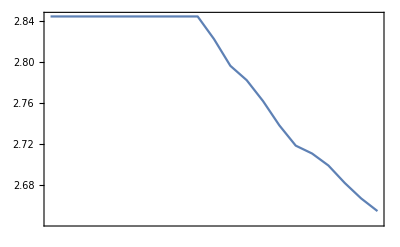

```mathematica
DateListPlot[timeseries]
```

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Luigi Brancati

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Mutual Information

Data Analysis

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

DistanceFunction

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

[1] Kraskov et al., Estimating mutual information

[2] Estimation of mutual information for real-valued data with error bars and controlled bias

[3] On Complexity and Efficiency of Mutual Information Estimation on Static and Dynamic Data

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

Link to other related material

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

The functions MutualIformation[list,list] and MutualInformation[list,_] are quite slow due to the amount of distances that needs to be computed. It has at the very best complexity of n*Log(n) [3]

I would like to extend it to TimeSeries.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Mutual Information should be always positive, but the estimator must not. It may happen that for weakly correlated data and few data points the value is negative.
The estimator itself is asymptotically unbiased, so on large datasets it doesn't depend on the specific distance used or on the value of k.